Created by: ruebenko on 01-08-2019 10:52:17

### Categorization

Tutorial

Synonyms

### Keywords

Multi region

material region

flow

silicon

anemometer

heat

heat equation

manual mesh

manual geometry

Details

# Anemometer

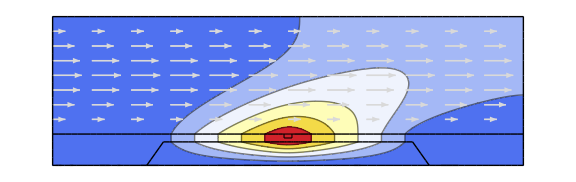

```mathematica
pts=Flatten[Table[{x,y},{x,0,1100,100},{y,anemometerHight,anemometerHight+flowHight,flowHight/8}],1];
Show[
ContourPlot[ifun[x,y],{x,y}∈MeshRegion[mesh]["MakeLinear"],AspectRatio->Automatic,ColorFunction->"TemperatureMap",PlotRange->All,Mesh->None,Axes->False,Frame->False],
VectorPlot[ Flatten[ convectionFunction[x,y]/.ElementMarker->4 ] ,{x,baseX,anemometerLength+additionalModelLength},{y,anemometerHight,anemometerHight+flowHight}, Frame->False,VectorScale->Small,VectorPoints->pts,VectorStyle->{{LightGray,"Arrow"}},VectorMarkers->Placed["Arrow","Start"]],
ToBoundaryMesh[mesh]["Wireframe"]
,ImageSize->Large]
```

In this application an anemometer is simulated. An anemometer is a device that can be attached to fluid flowing through, say, a pipe and measure the flow velocity in a contact less manner. For this a small section in the device is heated and the flow passing over the heater will distort the temperature profile generated by the heater. The distortion of the temperature profile can be measured and from the difference in temperature the velocity of the fluid passing the device can be computed.

Here is a sketch of the device. The device (in gray) is made of silicon and has a small heater (red) also made of silicon embedded. We have air (blue) passing over the device. The lower blue part is also air but no flow field is present there.

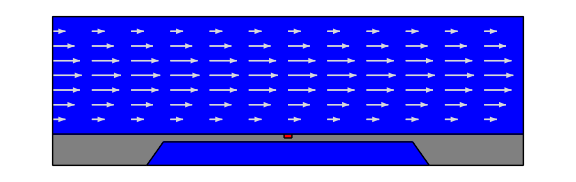

```mathematica
pts=Flatten[Table[{x,y},{x,0,1100,100},{y,anemometerHight,anemometerHight+flowHight,flowHight/8}],1];
Show[
mesh["Wireframe"["MeshElementStyle"->{Directive[FaceForm[Gray],EdgeForm[]],Directive[FaceForm[Red],EdgeForm[]],Directive[FaceForm[Blue],EdgeForm[]],Directive[FaceForm[Blue],EdgeForm[]]}]],
VectorPlot[ Flatten[ convectionFunction[x,y]/.ElementMarker->4 ] ,{x,baseX,anemometerLength+additionalModelLength},{y,anemometerHight,anemometerHight+flowHight}, Frame->False,VectorScale->Small,VectorPoints->pts,VectorStyle->{{LightGray,"Arrow"}},VectorMarkers->Placed["Arrow","Start"]],
bMesh["Wireframe"],ImageSize->Large]
```

To model the device a convection diffusion equation is used:

∇·(-c ∇u) +β·∇u=f.

The coefficients c, β and f will have different values in different material regions in the simulation domain. c is a diffusion coefficient and is active in the entire simulation domain, however, different values apply in different regions. β is a convection coefficient and is only active where the fluid is flowing over the device. f is a load coefficient and will be used to model the heater in the device.

We start by manually setting up a boundary geometry. First some device parameters like sizes and angles are set up.

Set up parameters.

```mathematica
baseX=baseY=0 ;
anemometerLength=1200;
additionalModelLength=anemometerLength;
additionalModelLength=0;
anemometerHight=80;
anemometerBase=240;
membraneThick=20;
heatLength=20;
heatHight=10;
flowHight=300;
```

α is the angle for the cut out in the silicon.

Additional parameters.

```mathematica
alpha=ArcTan[Sqrt[2.]];
myBeta=Pi/2-alpha;
membraneHight=(anemometerHight-membraneThick);
l1=membraneHight/Sin[alpha]*Sin[myBeta];
```

The coordinates for the boundary mesh.

```mathematica
p1={baseX, baseY};
p2=p1+{anemometerBase, 0};
p5=p2+{l1, membraneHight};
p4=p1+{anemometerLength, 0};
p3=p4-{anemometerBase, 0};
p6=p3-{l1,-membraneHight};
p9=p1+{0, anemometerHight};
p12=p4+{0, anemometerHight};
heatBase=(p12-p9 )/2-{heatLength/2,-(anemometerHight- heatHight)};
p7=heatBase;
p8=heatBase+{heatLength, 0};
p10=heatBase+{0, heatHight};
p11=heatBase+{heatLength, heatHight};
p13=p1+{0, anemometerHight+flowHight};
p14=p13+{anemometerLength+additionalModelLength, 0};
```

Group the coordinates together.

```mathematica
inCoords={p1, p2, p3, p4, p5, p6, p7, p8, p9, p10, p11, p12, p13, p14};
```

Create the boundary segments that provide the information how the coordinates are connected.

```mathematica
siliconIN={{1,2},{2,5},{5,6},{6,3},{3,4},{4,12},{12,11},{11,10},{10,9},{9,1}};
heaterIN={{10,7},{7, 8},{8, 11}};
flowBoxIN={{12,14},{14,13},{13,9}};
freeCutIN={{2,3}};
```

Group the segments.

```mathematica
deviceIN=Join[siliconIN,heaterIN,flowBoxIN,freeCutIN];
```

Visualize a graphics of the device.

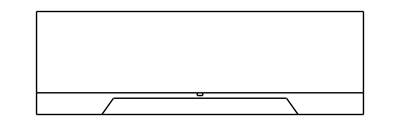

```mathematica
Graphics[GraphicsComplex[inCoords, Line/@deviceIN]]
```

Now, that we have coordinates of the boundary geometry markers are added to facilitate the application of boundary conditions and different material parameters in the device. A detailed introduction to markers is given in a section about markers in the ElementMesh generation tutorial.

Load the Finite Element package.

```mathematica
Needs["NDSolve`FEM`"]
```

Set up boundary markers.

```mathematica
siliconMarker={1,7,7,7,1,7,7,7,7,7};
heaterMarker={7,7,7};
flowBoxMarker={2,4,3};
freeCutMarker={1};
```

Group the markers.

```mathematica
deviceMarker=Join[siliconMarker,heaterMarker,flowBoxMarker,freeCutMarker];
```

```mathematica
Partition[Range[Length[inCoords]],1]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14}}

Set up the point element incidents and markers.

```mathematica
pointIncidents=Partition[Range[Length[inCoords]],1];
pointMarkers={1,1,1,1,7,7,7,7,7,7,7,7,4,4};
```

Create the boundary mesh.

```mathematica
bMesh=ToBoundaryMesh["Coordinates"->inCoords, "BoundaryElements"->{LineElement[deviceIN,deviceMarker]},
"PointElements"->{PointElement[pointIncidents,pointMarkers]}]
```

ElementMesh[{{0.,1200.},{0.,380.}},Automatic]

Inspect the point markers.

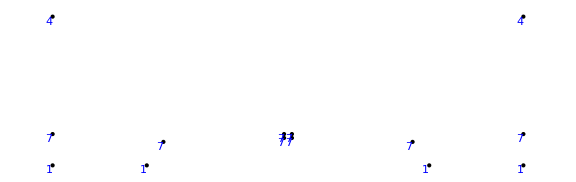

```mathematica
bMesh["Wireframe"["MeshElement"->"PointElements","MeshElementMarkerStyle"->Blue,ImageSize->Large]]
```

Inspect the boundary markers.

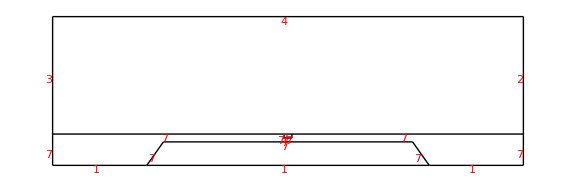

```mathematica
bMesh["Wireframe"["MeshElement"->"BoundaryElements","MeshElementMarkerStyle"->Red,ImageSize->Large]]
```

Now, that a boundary mesh is set up the full mesh is constructed. The boundary mesh is augmented with region markers. These are specified by a coordinate point inside the respective sub-region, an integer marker and a specification for the amount of refinement in that sub-region.

Generate coordinates in the different sub-regions.

```mathematica
p17=p1+{anemometerLength /2, (anemometerHight-membraneThick)/2};
p18=p1+{anemometerLength/2, anemometerHight-heatHight-(membraneThick-heatHight)/2};
p19=p1+{anemometerLength/2, anemometerHight-heatHight/2};
p20=p1+{anemometerLength/2, anemometerHight+flowHight/2};
```

Visualize the marker coordinates in the boundary mesh.

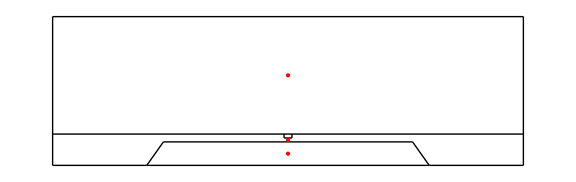

```mathematica
Show[bMesh["Wireframe"[ImageSize->Large]],Graphics[{Red,Point[#]}&/@{p17,p18,p20}]]
```

Generate the full mesh with region markers and specified mesh element refinement sizes.

```mathematica
mesh=ToElementMesh[bMesh,"RegionMarker"->Transpose[ {{p17, p18, p19, p20},{3,1,2,4}, {200., 200., 0.1, 200.}}]]
```

ElementMesh[{{0.,1200.},{0.,380.}},{TriangleElement[<7706>]}]

Visualize the mesh with air in blue, silicon in gray and the heater in read.

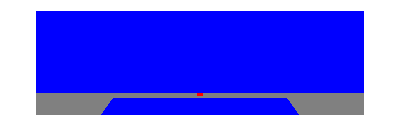

```mathematica
mesh["Wireframe"["MeshElementStyle"->{Directive[FaceForm[Gray],EdgeForm[]],Directive[FaceForm[Red],EdgeForm[]],Directive[FaceForm[Blue],EdgeForm[]],Directive[FaceForm[Blue],EdgeForm[]]}]]
```

All in all, we have four different parts in the simulation domain. The silicon device, the heater, to flow region and the cut out underneath the silicon. The material data for the silicon and the heater is the same and so is the air above and below the silicon.

Inspect the region markers.

```mathematica
mesh["MeshElementMarkerUnion"]
```

{1,2,3,4}

Visualize the part of the mesh that has ElementMarker set to 1.

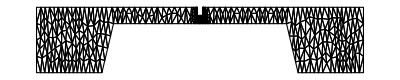

```mathematica
mesh["Wireframe"[ElementMarker==1]]
```

Next the material data is set up. The material data will have different values in different sub-regions of the device.

Setup the anisotropy.

```mathematica
anisotropyScale=1./10^6;
aniso1=anisotropyScale * 148. * {{1,0},{0,1}};
aniso2=anisotropyScale * 0.0239 * {{1,0},{0,1}};
anisotropyFunction=With[{aniso1=aniso1, aniso2=aniso2},If[ ElementMarker==1||ElementMarker==2,aniso1,aniso2]]
```

If[ElementMarker==1||ElementMarker==2,{{0.000148,0.},{0.,0.000148}},{{2.39×10^-8,0.},{0.,2.39×10^-8}}]

Set up the convection.

```mathematica
convectionScale=1./10^12.;
velocity=1.;
convF=Function[y,Evaluate[
- convectionScale *  {{1040*0.616*velocity* ( ( (y-( anemometerHight+flowHight/2))/(flowHight/2))^2-1.),0.}}] ];
convectionFunction[x_,y_] := Evaluate[ With[{conv=convF[y]},If[ElementMarker == 4, conv,{{0., 0.}} ]]]
```

Plot the convection flow profile.

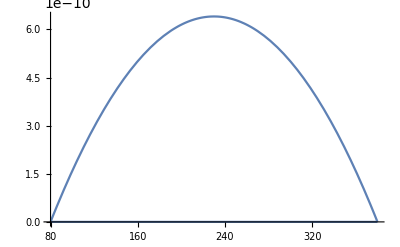

```mathematica
Plot[ convectionFunction[x,y]/.ElementMarker->4, {y,anemometerHight,anemometerHight+flowHight} ]
```

Visualize the flow field above the silicon.

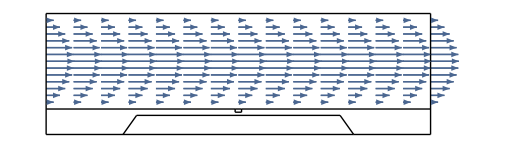

```mathematica
vectorField=Show[{VectorPlot[ Flatten[ convectionFunction[x,y]/.ElementMarker->4 ] ,{x,baseX,anemometerLength+additionalModelLength},{y,anemometerHight,anemometerHight+flowHight}, Frame->False,VectorMarkers->Placed["Arrow","Start"]],
bMesh["Wireframe"]},
PlotRange -> All,AspectRatio->Automatic]
```

Set up the load.

```mathematica
loadScale=1./10^12;
loadL=loadScale * 10^7.;
loadFunction=With[{loadL=loadL},If[ElementMarker==2,loadL,0.]]
```

If[ElementMarker==2,0.00001,0.]

Set up the boundary conditions.

```mathematica
bcs=DirichletCondition[u[x,y]==0.,ElementMarker==1||ElementMarker==3];
```

Solve the partial differential equation.

```mathematica
ifun=NDSolveValue[{-Inactive[Div][anisotropyFunction.Inactive[Grad][u[x,y],{x,y}],{x,y}]+convectionFunction[x,y].Inactive[Grad][u[x,y],{x,y}]==loadFunction,bcs},u,{x,y}∈mesh];
```

Visualize the solution.

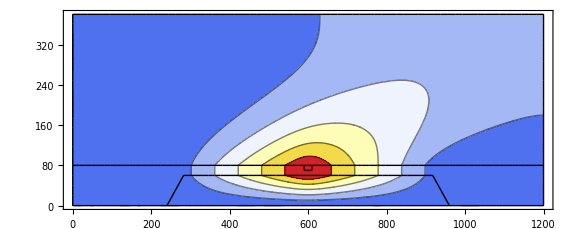

```mathematica
Show[
ContourPlot[ifun[x,y],{x,y}∈MeshRegion[mesh]["MakeLinear"],AspectRatio->Automatic,ColorFunction->"TemperatureMap",PlotRange->All,Mesh->None,Axes->False],
ToBoundaryMesh[mesh]["Wireframe"]
,ImageSize->Large]
```

Compute the minimum and maximum temperatures.

```mathematica
MinMax[ifun["ValuesOnGrid"]]
```

{0.,119.571}

Compute the temperature difference between to points on the device.

```mathematica
ifun[400,80]-ifun[800,80]
```

-0.0634534

More About

Related Tutorials

Related Wolfram Training Courses